## 1. Imports and Definitions

We need to import finite elements directly to have access to some functions

```mathematica
<<NDSolve`FEM`
```

The greatest function ever created, reference cell block directly above

```mathematica
«:=Out[
ToExpression[
StringCases[
ToString[PreviousCell[CellStyle->"Output"]//NotebookRead//Last],
"Out["~~d:DigitCharacter..~~"]":>d][[1]]
]
]
```

Fancy formatting rules

```mathematica
Format[
z0
]:="z_0"
Format[
cQ
]:="c_Q"
```

```mathematica
Format[
Vxaux[X,Y,Z]
]:="V_x"
Format[
D[
	Vxaux[X,Y,Z], 
	{X, n_},
	{Y, m_},
	{Z, l_}
]
] := ("(|01d715)_X")^n("(|01d715)_Y")^m("(|01d715)_Z")^l HoldForm["V_x"]
```

```mathematica
Format[
Vyaux[X,Y,Z]
]:="V_y"
Format[
D[
	Vyaux[X,Y,Z], 
	{X, n_},
	{Y, m_},
	{Z, l_}
]
] := ("(|01d715)_X")^n("(|01d715)_Y")^m("(|01d715)_Z")^l HoldForm["V_y"]
```

## 2. Equations

The PDE’s we’re gonna solve are
	ΔV_x=(c_Q z_0 y)/(|(r⃗)_-|^3|(r⃗)_+|^3)
	ΔV_y=-(c_Q z_0 x)/(|(r⃗)_-|^3|(r⃗)_+|^3)

where (r⃗)_- and (r⃗)_+are
	(r⃗)_-={x,y,z+z_0}
(r⃗)_+={x,y,z-z_0}

We’re going to use the compactification
	x=k X^n/((1-X^2)^((n+1)/2))
	y=k Y^n/((1-Y^2)^((n+1)/2))
	z=k Z^n/((1-Z^2)^((n+1)/2))

where n=1,3,5,...

Define (r⃗)_- and (r⃗)_+

```mathematica
rm:={x,y,z+z0};
rp:={x,y,z-z0};
```

Define the independent variables, already in compactified coordinates

```mathematica
Vx:=Vxaux[X,Y,Z]
Vy:=Vyaux[X,Y,Z]
```

Compactification {x, y, z } -> {X, Y, Z } is

```mathematica
compactify:={
	x->k X^n/((1-X^2)^((n+1)/2)),y->k Y^n/((1-Y^2)^((n+1)/2)),z->k Z^n/((1-Z^2)^((n+1)/2))
};
```

The partial derivatives of {x, y, z } as a function of compactified coordinates { X, Y, Z } are

```mathematica
PDx[u_]:=(X^(1-n) (1-X^2)^((3+n)/2))/(k (n+X^2))D[(u), X];
PDy[u_]:=(Y^(1-n) (1-Y^2)^((3+n)/2))/(k (n+Y^2))D[(u), Y];
PDz[u_]:=(Z^(1-n) (1-Z^2)^((3+n)/2))/(k (n+Z^2))D[(u), Z];
```

The compactified PDEs are

```mathematica
PDEx=(k^2(PDx[PDx[Vx]]+PDy[PDy[Vx]]+PDz[PDz[Vx]])//FullSimplify)-(k^2(cQ z0 y)/((rm.rm)^(3/2)(rp.rp)^(3/2))/.compactify//FullSimplify)
```

-((c_Q k^3 Y^n (1-Y^2)^(-1/2-n/2) z_0)/((k^2 X^(2 n) (1-X^2)^(-1-n)+k^2 Y^(2 n) (1-Y^2)^(-1-n)+(-k Z^n (1-Z^2)^(-1/2-n/2)+z_0)^2)^(3/2) (k^2 X^(2 n) (1-X^2)^(-1-n)+k^2 Y^(2 n) (1-Y^2)^(-1-n)+(k Z^n (1-Z^2)^(-1/2-n/2)+z_0)^2)^(3/2)))-(Z^(1-2 n) (1-Z^2)^(2+n) ((-1+n) n+(1+5 n) Z^2+2 Z^4) (𝜕_Z V_x))/((n+Z^2)^3)+(Z^(2-2 n) (1-Z^2)^(3+n) ((𝜕_Z)^2 V_x))/((n+Z^2)^2)+(Y^(1-2 n) (1-Y^2)^n (n-Y^2+6 Y^4-6 Y^6+2 Y^8) (𝜕_Y V_x))/((n+Y^2)^3)-(Y^(1-2 n) (1-Y^2)^n ((n-2 (-3+n) Y^2+(-9+n) Y^4+4 Y^6) (𝜕_Y V_x)+Y (-1+Y^2)^3 ((𝜕_Y)^2 V_x)))/((n+Y^2)^2)+(X^(1-2 n) (1-X^2)^n (n-X^2+6 X^4-6 X^6+2 X^8) (𝜕_X V_x))/((n+X^2)^3)-(X^(1-2 n) (1-X^2)^n ((n-2 (-3+n) X^2+(-9+n) X^4+4 X^6) (𝜕_X V_x)+X (-1+X^2)^3 ((𝜕_X)^2 V_x)))/((n+X^2)^2)

```mathematica
PDEy=(k^2(PDx[PDx[Vy]]+PDy[PDy[Vy]]+PDz[PDz[Vy]])//FullSimplify)+(k^2(cQ z0 x)/((rm.rm)^(3/2)(rp.rp)^(3/2))/.compactify//FullSimplify)
```

(c_Q k^3 X^n (1-X^2)^(-1/2-n/2) z_0)/((k^2 X^(2 n) (1-X^2)^(-1-n)+k^2 Y^(2 n) (1-Y^2)^(-1-n)+(-k Z^n (1-Z^2)^(-1/2-n/2)+z_0)^2)^(3/2) (k^2 X^(2 n) (1-X^2)^(-1-n)+k^2 Y^(2 n) (1-Y^2)^(-1-n)+(k Z^n (1-Z^2)^(-1/2-n/2)+z_0)^2)^(3/2))-(Z^(1-2 n) (1-Z^2)^(2+n) ((-1+n) n+(1+5 n) Z^2+2 Z^4) (𝜕_Z V_y))/((n+Z^2)^3)+(Z^(2-2 n) (1-Z^2)^(3+n) ((𝜕_Z)^2 V_y))/((n+Z^2)^2)+(Y^(1-2 n) (1-Y^2)^n (n-Y^2+6 Y^4-6 Y^6+2 Y^8) (𝜕_Y V_y))/((n+Y^2)^3)-(Y^(1-2 n) (1-Y^2)^n ((n-2 (-3+n) Y^2+(-9+n) Y^4+4 Y^6) (𝜕_Y V_y)+Y (-1+Y^2)^3 ((𝜕_Y)^2 V_y)))/((n+Y^2)^2)+(X^(1-2 n) (1-X^2)^n (n-X^2+6 X^4-6 X^6+2 X^8) (𝜕_X V_y))/((n+X^2)^3)-(X^(1-2 n) (1-X^2)^n ((n-2 (-3+n) X^2+(-9+n) X^4+4 X^6) (𝜕_X V_y)+X (-1+X^2)^3 ((𝜕_X)^2 V_y)))/((n+X^2)^2)

## 3. Solve PDEs

```mathematica
params={
	cQ->1,
	z0->1,
	k->1,
	n->1
};
```

```mathematica
sol=NDSolve[
	{
		PDEx==NeumannValue[0,X==-1]+NeumannValue[0,X==1]+NeumannValue[0,Y==-1]+NeumannValue[0,Y==1]+NeumannValue[0,Z==-1]+NeumannValue[0,Z==1]/.params,
		Vxaux[1,Y,Z]   ==0,
		Vxaux[-1,Y,Z] ==0,
		Vxaux[X,-1,Z] ==0,
		Vxaux[X,1,Z]   ==0,
		Vxaux[X,Y,1]   ==0,
		Vxaux[X,Y,-1] ==0
	},
	Vxaux,
	{X,-1,1},
	{Y,-1,1},
	{Z,-1,1}
]
```

NDSolve::femcnsd: The PDE coefficient Y/((1-Y^2) (X^2/(1-«1»)^2+Y^2/(«1»)^2+(1-Z/(«1»))^2)^(3/2) (X^2/(1-«1»)^2+Y^2/(1-«1»)^2+(1+Z/(«1»))^2)^(3/2)) does not evaluate to a numeric scalar at the coordinate {-1.,-1.,-1.}; it evaluated to Indeterminate instead.

NDSolve[{-Y/((1-Y^2) (X^2/((1-X^2)^2)+Y^2/((1-Y^2)^2)+(1-Z/(1-Z^2))^2)^(3/2) (X^2/((1-X^2)^2)+Y^2/((1-Y^2)^2)+(1+Z/(1-Z^2))^2)^(3/2))-((1-Z^2)^3 (6 Z^2+2 Z^4) (𝜕_Z V_x))/(Z (1+Z^2)^3)+((1-Z^2)^4 ((𝜕_Z)^2 V_x))/((1+Z^2)^2)+((1-Y^2) (1-Y^2+6 Y^4-6 Y^6+2 Y^8) (𝜕_Y V_x))/(Y (1+Y^2)^3)-((1-Y^2) ((1+4 Y^2-8 Y^4+4 Y^6) (𝜕_Y V_x)+Y (-1+Y^2)^3 ((𝜕_Y)^2 V_x)))/(Y (1+Y^2)^2)+((1-X^2) (1-X^2+6 X^4-6 X^6+2 X^8) (𝜕_X V_x))/(X (1+X^2)^3)-((1-X^2) ((1+4 X^2-8 X^4+4 X^6) (𝜕_X V_x)+X (-1+X^2)^3 ((𝜕_X)^2 V_x)))/(X (1+X^2)^2)==NeumannValue[0,X==-1]+NeumannValue[0,X==1]+NeumannValue[0,Y==-1]+NeumannValue[0,Y==1]+NeumannValue[0,Z==-1]+NeumannValue[0,Z==1],Vxaux[1,Y,Z]==0,Vxaux[-1,Y,Z]==0,Vxaux[X,-1,Z]==0,Vxaux[X,1,Z]==0,Vxaux[X,Y,1]==0,Vxaux[X,Y,-1]==0},Vxaux,{X,-1,1},{Y,-1,1},{Z,-1,1}]

## A. Sketches

```mathematica
(* haveria de fazer um apendice onde calculo as ∂_x em funcao de ∂_X so pa ficar escrito *)
```

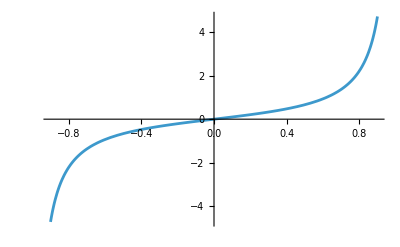

```mathematica
Plot[
	Y/(1-Y^2),
	{Y,-0.9,0.9}
]
```

```mathematica
Solve[
	y==k Y^n/((1-Y^2)^((n+1)/2)),
	Y
]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Solve[y==k Y^n (1-Y^2)^(1/2 (-1-n)),Y]

```mathematica
D[(k Y^n/((1-Y^2)^((n+1)/2))), Y]//FullSimplify
```

k Y^(-1+n) (1-Y^2)^(1/2 (-3-n)) (n+Y^2)

```mathematica
1/«//FullSimplify
```

(Y^(1-n) (1-Y^2)^((3+n)/2))/(k (n+Y^2))

```mathematica
Solve[
	D[(k Y^n/((1-Y^2)^((n+1)/2))), Y]==0//FullSimplify,
	Y
]
```

{{Y→ⅈ √n}}

```mathematica
(**********************************************
```

```mathematica
PDEx/.params
```

-Y/((1-Y^2) (X^2/((1-X^2)^2)+Y^2/((1-Y^2)^2)+(1-Z/(1-Z^2))^2)^(3/2) (X^2/((1-X^2)^2)+Y^2/((1-Y^2)^2)+(1+Z/(1-Z^2))^2)^(3/2))-((1-Z^2)^3 (6 Z^2+2 Z^4) (𝜕_Z V_x))/(Z (1+Z^2)^3)+((1-Z^2)^4 ((𝜕_Z)^2 V_x))/((1+Z^2)^2)+((1-Y^2) (1-Y^2+6 Y^4-6 Y^6+2 Y^8) (𝜕_Y V_x))/(Y (1+Y^2)^3)-((1-Y^2) ((1+4 Y^2-8 Y^4+4 Y^6) (𝜕_Y V_x)+Y (-1+Y^2)^3 ((𝜕_Y)^2 V_x)))/(Y (1+Y^2)^2)+((1-X^2) (1-X^2+6 X^4-6 X^6+2 X^8) (𝜕_X V_x))/(X (1+X^2)^3)-((1-X^2) ((1+4 X^2-8 X^4+4 X^6) (𝜕_X V_x)+X (-1+X^2)^3 ((𝜕_X)^2 V_x)))/(X (1+X^2)^2)

```mathematica
1/(X/(1-X^2))/.{X->1}
```

0

```mathematica
1/(1/(1-X^2)+1/(1-Y^2))/.{X->1,Y->1}
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Indeterminate